## Derivation of scattering contributions from a random-walk polymer ring.

```mathematica
$Assumptions:={L>0,l>=0,l<= L,b>0,q>0,Re[l (l-L)]<0}
```

#### Ring polymer model

The statistics of a polymer of contour length l, and step length b can be mapped to a harmonic spring with a spring constant k(l)=3kT/b l where U(R)=1/2 k R^2 and the corresponding Boltzmann distribution is the Gaussian end-to-end distribution of the corresponding polymer.

A polymer ring then becomes equivalent to two springs connecting origo to a position at coordinate R, but since the total contour length of the polymer is L, one polymer has length l and the other has L-l. Where we have to average l over an uniform distribution of l afterwards. In one realization with l and L-l. Secondly I use spherical coordinates, since the probability only depend on the distance R and not the coordinate.

```mathematica
Uring[R_,l_]=1/2(3kT)/(b l)R^2+1/2(3kT)/(b (L-l))R^2//Simplify
```

-(3 kT L R^2)/(2 b l^2-2 b l L)

```mathematica
Z=Integrate[Exp[-Uring[R,l]/kT]4π R^2,{R,0,Infinity}]
```

2/3 √(2/3) ((b l (-l+L))/L)^(3/2) π^(3/2)

The distribution involves an integral that can not be evaluated to closed form:

```mathematica
P[R_,L_]=Integrate[1/(Z L)Exp[-Uring[R,l]/kT]4π R^2,{l,0,L}]
```

∫_0^L (3 ⅇ^((3 L R^2)/(2 b l^2-2 b l L)) √(6/π) R^2)/(L ((b l (-l+L))/L)^(3/2))ⅆl

The phase factor between origo and the point at R for a fixed L - l, l configuration is :

```mathematica
Psil=Integrate[1/Z Exp[-Uring[R,l]/kT] Sin[q R]/(q R) 4π R^2,{R,0,Infinity}]
```

ⅇ^((b l (l-L) q^2)/(6 L))

Averaging this over the uniform distribution of l in [0 : L] :

```mathematica
Psi=Integrate[1/L Psil,{l,0,L}]
```

(ⅇ^(-1/24 b L q^2) √(6 π) Erfi[(√(b L) q)/(2 √6)])/(√(b L) q)

And now we are done . We could have chosen any other point on the loop as Origo, the loop would be the same due to translational invariance along the loop . Hence the form factor between any pairs of points, the form factor amplitude relative to any point we choose as origio and any other randomly chosen point, and finally the phase factor between two randomly chosen points are all given by this expression .

We choose x=q √((b L)/24) =q Rg √(1/2) is a good dimensionless variable. Furthermore,introducin the Dawson integral simply the expression compared to Erfi, which Mathematica likes.

```mathematica
F(x)==exp(-x^2) ∫_0^x exp(y^2)ⅆy
```

```mathematica
FunctionExpand[DawsonF[x]]
```

1/2 ⅇ^(-x^2) √π Erfi[x]

```mathematica
Solve[DawsonF[x]==1/2 ⅇ^(-x^2) √π Erfi,Erfi]
```

{{Erfi→(2 ⅇ^(x^2) DawsonF[x])/(√π)}}

```mathematica
Fring[x_]=Psi/.q->x √(24/(b L))/.Erfi[x_]->(2 ⅇ^(x^2) DawsonF[x])/(√π)//PowerExpand
```

DawsonF[x]/x

```mathematica
Series[%,{x,0,6}]
```

1-(2 x^2)/3+(4 x^4)/15-(8 x^6)/105+O[x]^7

```mathematica
Series[DawsonF[x],{x,0,6}]
```

x-(2 x^3)/3+(4 x^5)/15+O[x]^7

```mathematica
Reference : Casassa EF (1965) Some statistical properties of flexible ring polymers . J Polym Sci Part A 3 (2 pa) : 605 - 614.
http://dx.doi.org/10.1002/pol.1965.100030217
```

Reference:11790 A Casassa EF flexible of pa Part Polym properties ring Sci Some statistical polymers.J:-9.

Syntax::sntxf: "" cannot be followed by "ence : Casassa EF (1965) Some statistical properties of flexible
      ring polymers . J Polym Sci Part A 3 (2 pa) : 605 - 614.".

(0.00194609 dx.doi.org)/pol

```mathematica
NB there is a bug in the equation in C . Svaneborg, J . S . Pedersen J . Chem . Phys . 136, 154907 (2012); doi : 10.1063/1.3701737 :
```

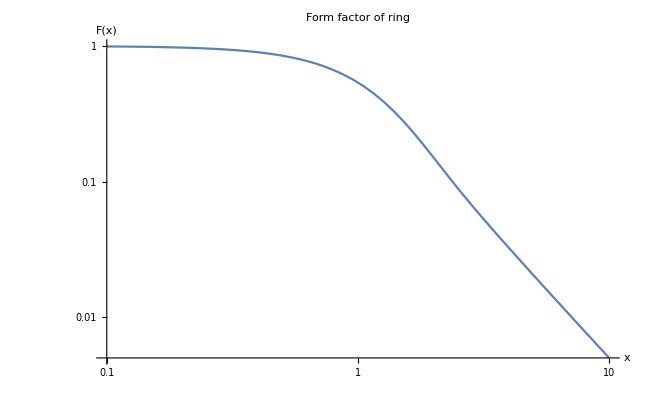

```mathematica
LogLogPlot[Fring,{x,0.1,10},PlotLabel->"Form factor of ring",AxesLabel-> {"x","F(x)"}]
```

Some numerical values for comparison examples :

```mathematica
Fring[0.1]
Fring[0.5]//N
Fring[1]//N
Fring[10]//N
```

0.99336

0.848873

0.53808

0.00502538

#### Lets now calculate all the relevant mean - square distance measures explicitly

Mean - square distance between one at 0, and another at l in [0:L]. I divide by a factor of two, since we are double counting since l and L-l are the same pair distance along the chain:

```mathematica
Integrate[1/(2 L)1/Z Exp[-Uring[R,l]/kT] 4π R^2 R^2,{R,0,Infinity},{l,0,L}]
```

(b L)/12

Alternatively, we only integrate to l in [0 : L/2] to stop double counting :

```mathematica
Integrate[1/L 1/Z Exp[-Uring[R,l]/kT] 4π R^2 R^2,{R,0,Infinity},{l,0,L/2}]
```

(b L)/12

These are consistent with known theory for loops . See e . g . B. Hammouda “Form Factors for Branched Polymers with
Excluded Volume”  http://dx.doi.org/10.6028/jres.121.006

#### Guinier - expansions

Above we derived the mean - square distances explicitly. Here we show how to obtain these from a Guinier expansion of the various scattering terms.

The Guinier expansion of F is
1 - q^2 Rg^2 / 3 + O(q^4)

```mathematica
Series[Fring/.x->q Rg √(1/2),{q,0,3}]
```

1-(Rg^2 q^2)/3+O[q]^4

Hence to isolate the radius of gyration in the series:

```mathematica
(3(1-Normal[Series[Fring/.x->q Rg √(1/2),{q,0,3}]]))/q^2
```

Rg^2

For σ < R^2 > distances between random pairs along the loop :

```mathematica
(6(1-Normal[Series[Fring/.x->q Rg √(1/2),{q,0,3}]]))/q^2
```

2 Rg^2

#### Save example data to file for Validation :

```mathematica
SaveFunction[func_,filename_,NN_,qmin_,qmax_]:=Module[{},Export[filename,{#,N[func/.q-> #]}&/@Table[10^(Log[10,qmax/qmin]*i/NN+Log[10,qmin]),{i,0,NN}]]]
```

```mathematica
SaveFunction[Fring[q Rg √(1/2)/.Rg->1 ],"/home/zqex/source/SEB/source/Validation/RWloop_mathematica/F.dat",200,0.01,20]
```

/home/zqex/source/SEB/source/Validation/RWloop_mathematica/F.dat